# Math2200: Applied Mathematics

## 2009 Semester 1 — Final Exam

Student ID = Solutions                                                                                 Total Mark = mark

## Section. Instructions:

Time allowed : 3 hours

TYPE YOUR STUDENT NUMBER IN THE BOX PROVIDED

Save your notebook now and save regularly during the test.
Save either on the network server in the MCL or to a memory stick, in case your computer crashes.

This is an “open-book” exam. You are permitted to bring in printed or electronic copies of your lecture notes and assignment solutions, and to access electronic resources such as the Documentation Center and the internet.

Spoken or electronic communication via email, messaging, chat, file transfer, etc. is not permitted. Such action may result in your being deprived of any credit for this examination or even, in some cases, for the whole unit. This will apply regardless of whether the material has been used at the time it is found.

Insert your solutions—both Mathematica code and text—directly into the Notebook below the Solution cell that immediately follows the part of the question that you are answering.

When asked to do so by the examination supervisor, upload your solutions using the file name student#.nb to the Exam folder on the Physics FTP server.  (Follow normal path from the desktop with "student" username.)
Stay seated and do not talk until the examination supervisors verify that the correct number of notebooks have been uploaded.

## Section. Mathematica calculations and programming. [20 Marks]

Question SectionExercise)   [4 Marks]

One of the most important steps in using Mathematica is translating a given problem into useful Mathematica code.   Our first, example comes from Chemistry.

The first step in the production of chromium metal from the chromite ore, Fe Cr_2 O_4 is the following reaction.

Fe Cr_2 O_4 + Na_2 CO_3+O_2 ⟶^(+ heat) Na_2Cr O_4+Fe_2 O_3+CO_2

In this reaction the iron is oxidised from its 2+ form to its 3+ form, the carbonate decomposes to carbon dioxide and the dichromate ion is changed to a chromate ion.  The above is not a balanced reaction.   Use Mathematica to find the smallest positive integers x_1,…,x_6 such that all atomic species in

x_1 Fe Cr_2 O_4 + x_2 Na_2 CO_3+x_3 O_2 ⟶^(+ heat) x_4 Na_2 Cr O_4+x_5 Fe_2 O_3+x_6 CO_2

are balanced.  The last line in your code should output the list of integers {x_1,x_2,x_3,x_4,x_5,x_6}.   [4 Marks]

Hint/Clarification:  There are six unkown coefficients and five atomic species above: Iron—Fe, Chromium—Cr, Oxygen—O, Sodium—Na and Carbon—C.
If you need some more clarifaction or examples, look here:  http://en.wikipedia.org/wiki/Chemical_equation.

Solution:

This question came from http://en.wikipedia.org/wiki/Dichromate.

The balanced equation is:

4Fe Cr_2 O_4 + 8 Na_2 CO_3+7O_2 ⟶^(+ heat) 8 Na_2 Cr O_4+2 Fe_2 O_3+8 CO_2

we will outline a few approaches here.

```mathematica
chemEqn=Subscript[x, 1] (Fe+2Cr+4𝒪)+Subscript[x, 2](2Na+𝒞+3𝒪)+Subscript[x, 3](2𝒪)==Subscript[x, 4](2Na+Cr+4𝒪)+Subscript[x, 5](2Fe+3𝒪)+Subscript[x, 6](𝒞+2𝒪);
```

##### Method 1

Direct, but requires us to choose by hand the minimal solution with x_i∈ℤ

```mathematica
SolveAlways[chemEqn,{Cr,Fe,𝒪,𝒞,Na}]
{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}/.%⟦1⟧/.Subscript[x, 3]->7
```

{{x_2→(8 x_3)/7,x_4→(8 x_3)/7,x_1→(4 x_3)/7,x_5→(2 x_3)/7,x_6→(8 x_3)/7}}

{4,8,7,8,2,8}

##### Method 2

Not quite as direct, but gets us to a stage where we can us Reduce over the integers

```mathematica
Collect[Subtract@@chemEqn,{Cr,Fe,𝒞,𝒪,Na},Simplify]
```

Cr (2 x_1-x_4)+2 Na (x_2-x_4)+Fe (x_1-2 x_5)+𝒪 (4 x_1+3 x_2+2 x_3-4 x_4-3 x_5-2 x_6)+𝒞 (x_2-x_6)

```mathematica
CoefficientList[%,{Cr,Fe,𝒞,𝒪,Na}]//Flatten
```

{0,2 (x_2-x_4),4 x_1+3 x_2+2 x_3-4 x_4-3 x_5-2 x_6,0,x_2-x_6,0,0,0,x_1-2 x_5,0,0,0,0,0,0,0,2 x_1-x_4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
And@@Thread[%==0]
Reduce[%,Integers]
```

2 (x_2-x_4)==0&&4 x_1+3 x_2+2 x_3-4 x_4-3 x_5-2 x_6==0&&x_2-x_6==0&&x_1-2 x_5==0&&2 x_1-x_4==0

C[1]∈Integers&&x_1==4 C[1]&&x_2==8 C[1]&&x_3==7 C[1]&&x_4==8 C[1]&&x_5==2 C[1]&&x_6==8 C[1]

```mathematica
%/.C[1]->1
```

x_1==4&&x_2==8&&x_3==7&&x_4==8&&x_5==2&&x_6==8

##### Method 3

This is basically the same as above, it's just we explicitly construct the system of equations by hand.
The rows correspond to the elements as they appear on the LHS of the reaction: Fe, Cr, O, Na and C

```mathematica
({{1, 0, 0}, {2, 0, 0}, {4, 3, 2}, {0, 2, 0}, {0, 1, 0}}).({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}})==({{0, 2, 0}, {1, 0, 0}, {4, 3, 2}, {2, 0, 0}, {0, 0, 1}}).({{Subscript[x, 4]}, {Subscript[x, 5]}, {Subscript[x, 6]}})//TraditionalForm
Reduce[Thread[%],Integers]
%/.C[1]->1
```

(x_1
2 x_1
4 x_1+3 x_2+2 x_3
2 x_2
x_2)==(2 x_5
x_4
4 x_4+3 x_5+2 x_6
2 x_4
x_6)

C[1]∈Integers&&x_1==4 C[1]&&x_2==8 C[1]&&x_3==7 C[1]&&x_4==8 C[1]&&x_5==2 C[1]&&x_6==8 C[1]

x_1==4&&x_2==8&&x_3==7&&x_4==8&&x_5==2&&x_6==8

##### Method 4

or, we can put it one big linear system and require

```mathematica
({{1, 0, 0, 0, -2, 0}, {2, 0, 0, -1, 0, 0}, {4, 3, 2, -4, -3, -2}, {0, 2, 0, -2, 0, 0}, {0, 1, 0, 0, 0, -1}}).({{Subscript[x, 1]}, {Subscript[x, 2]}, {Subscript[x, 3]}, {Subscript[x, 4]}, {Subscript[x, 5]}, {Subscript[x, 6]}})==0
```

ie, we're looking for

```mathematica
NullSpace@({{1, 0, 0, 0, -2, 0}, {2, 0, 0, -1, 0, 0}, {4, 3, 2, -4, -3, -2}, {0, 2, 0, -2, 0, 0}, {0, 1, 0, 0, 0, -1}})
```

{{4,8,7,8,2,8}}

Question SectionExercise)   [4 Marks]

Pattern matching is the core of most of Mathematica's functionality.  It is also a very powerful tool in a wide range of areas, as anyone who has used Regular Expressions would know.  In fact, the below exercise could be done with regular expressions or String Patterns.

Here are the first four sentences from the Grimm brothers ‘Rapunzel’, freely available from Project Guteneurg.

```mathematica
rapunzel="There were once a man and a woman who had long in vain wished for a child. At length the woman hoped that God was about to grant her desire. These people had a little window at the back of their house from which a splendid garden could be seen, which was full of the most beautiful flowers and herbs. It was, however, surrounded by a high wall, and no one dared to go into it because it belonged to an enchantress, who had great power and was dreaded by all the world.";
```

We can turn it into a list of single characters and remove non alphabetic characters using:

```mathematica
rapunzelList=Select[Characters[ToLowerCase[rapunzel]],MemberQ[CharacterRange["a","z"],#]&]
```

{t,h,e,r,e,w,e,r,e,o,n,c,e,a,m,a,n,a,n,d,a,w,o,m,a,n,w,h,o,h,a,d,l,o,n,g,i,n,v,a,i,n,w,i,s,h,e,d,f,o,r,a,c,h,i,l,d,a,t,l,e,n,g,t,h,t,h,e,w,o,m,a,n,h,o,p,e,d,t,h,a,t,g,o,d,w,a,s,a,b,o,u,t,t,o,g,r,a,n,t,h,e,r,d,e,s,i,r,e,t,h,e,s,e,p,e,o,p,l,e,h,a,d,a,l,i,t,t,l,e,w,i,n,d,o,w,a,t,t,h,e,b,a,c,k,o,f,t,h,e,i,r,h,o,u,s,e,f,r,o,m,w,h,i,c,h,a,s,p,l,e,n,d,i,d,g,a,r,d,e,n,c,o,u,l,d,b,e,s,e,e,n,w,h,i,c,h,w,a,s,f,u,l,l,o,f,t,h,e,m,o,s,t,b,e,a,u,t,i,f,u,l,f,l,o,w,e,r,s,a,n,d,h,e,r,b,s,i,t,w,a,s,h,o,w,e,v,e,r,s,u,r,r,o,u,n,d,e,d,b,y,a,h,i,g,h,w,a,l,l,a,n,d,n,o,o,n,e,d,a,r,e,d,t,o,g,o,i,n,t,o,i,t,b,e,c,a,u,s,e,i,t,b,e,l,o,n,g,e,d,t,o,a,n,e,n,c,h,a,n,t,r,e,s,s,w,h,o,h,a,d,g,r,e,a,t,p,o,w,e,r,a,n,d,w,a,s,d,r,e,a,d,e,d,b,y,a,l,l,t,h,e,w,o,r,l,d}

Your task is to find all palindromic sublists of length greater than 2.  (Note: the palindromes do not have to form real words.)  
Your replacement rules should return the palindrome and its starting position in the list.
For example, the first and the last palindrome in the list above are:
{"e", "r", "e"}  starting in the 3^rd position and {"d", "e", "d"} starting in the 352^nd position. [4 Marks]

Solution:

```mathematica
ReplaceList[rapunzelList,{a___,pal__,___}:>{Length[{a}]+1,{pal}}/;Reverse[{pal}]=={pal}&&Length[{pal}]>2]
```

{{3,{e,r,e}},{3,{e,r,e,w,e,r,e}},{4,{r,e,w,e,r}},{5,{e,w,e}},{7,{e,r,e}},{14,{a,m,a}},{16,{a,n,a}},{17,{n,a,n}},{28,{h,o,h}},{64,{t,h,t}},{65,{h,t,h}},{87,{a,s,a}},{112,{e,s,e}},{114,{e,p,e}},{122,{a,d,a}},{173,{d,i,d}},{188,{e,s,e}},{222,{l,f,l}},{246,{e,v,e}},{257,{d,e,d}},{268,{a,l,l,a}},{272,{n,d,n}},{274,{n,o,o,n}},{285,{o,g,o}},{314,{n,e,n}},{327,{h,o,h}},{352,{d,e,d}}}

We can remove all of the palindromes that are (central) subpalindromes of those above by

```mathematica
%//.{a___,o:{n_,{c__,pal__,d__}},{m_,{pal__}},b___}:>{a,o,b}/;m-n==Length[{c}]
```

{{3,{e,r,e}},{3,{e,r,e,w,e,r,e}},{7,{e,r,e}},{14,{a,m,a}},{16,{a,n,a}},{17,{n,a,n}},{28,{h,o,h}},{64,{t,h,t}},{65,{h,t,h}},{87,{a,s,a}},{112,{e,s,e}},{114,{e,p,e}},{122,{a,d,a}},{173,{d,i,d}},{188,{e,s,e}},{222,{l,f,l}},{246,{e,v,e}},{257,{d,e,d}},{268,{a,l,l,a}},{272,{n,d,n}},{274,{n,o,o,n}},{285,{o,g,o}},{314,{n,e,n}},{327,{h,o,h}},{352,{d,e,d}}}

Note: a slightly neater output is obtained by putting the substrings back together (unlike humpty dumpty)

```mathematica
ReplaceList[rapunzelList,{a___,pal__,___}:>{Length[{a}]+1,StringJoin[pal]}/;Reverse[{pal}]=={pal}&&Length[{pal}]>2]
```

{{3,ere},{3,erewere},{4,rewer},{5,ewe},{7,ere},{14,ama},{16,ana},{17,nan},{28,hoh},{64,tht},{65,hth},{87,asa},{112,ese},{114,epe},{122,ada},{173,did},{188,ese},{222,lfl},{246,eve},{257,ded},{268,alla},{272,ndn},{274,noon},{285,ogo},{314,nen},{327,hoh},{352,ded}}

Question SectionExercise)   [12 Marks]

One of the first and most useful formula you would have learnt in high-school algebra is the solution of a quadratic:

x^2+bx+c==0   ⟹   x=x_±=(-b±√(b^2-4c))/2

A result that is trivially reproduced and checked with Mathematica:

```mathematica
Reduce[x^2+b x+c==0,x]
```

x==1/2 (-b-√(b^2-4 c))||x==1/2 (-b+√(b^2-4 c))

We can think of this operation as a map, f, that takes two complex numbers, a and b, and returns the pair of complex numbers x_+ and x_-.  When we define this map, we have a choice of ordering to make: should it return (x_+,x_-) or (x_-,x_+)?  We'll define a map for each choice:

f_±:ℂ^2→ℂ^2 ,                         f_±:(b,c)↦((-b±√(b^2-4c))/2,(-b∓√(b^2-4c))/2)

Some examples  f_+(0,1)=(ⅈ,-ⅈ),  f_-(0,1)=(-ⅈ,ⅈ),  f_+(3,-4)=(1,-4), etc…

Now, in general, if we have a map that takes one object in a set to another in the set (in our case the objects are pairs of complex numbers) then we can iterate the map:

f:𝒮→𝒮:a↦f(a)
 f^(n)(a)=f(f^(n-1)(a))=… =f(f(f⋯f(a)))

If there exists an element p∈𝒮 such that f(p)=p, then p is called a fixed point of the map f.
If there exists an element q∈𝒮 and an integer ν>0 such that f^(ν)(q)=q then it must be that the sequence (q,f(q),… f^(ν-1)(q)) is repeated forever.  This is called a orbit or cycle of f with period ν.  An orbit with period 1 is a fixed point.

In the case of our maps f_± there is always the trivial fixed point f_±(0,0)=(0,0).  
Below, we will aslo investigate some other fixed points and orbits of our maps.  
It is also possible to investigate the behaviour of repeatedly applying various sequences of maps, such as a↦f_+(f_-(a)) etc…  
The existence and stability of the orbits of these more complicated maps is an open question.  
It can be shown that any combination of the maps f_± yield bounded sequences, 
the bound is illustrated in the picture on the right, that you will reproduce in part iv.3).  | -Graphics-

Define a function f({b,c},ord) that returns {x_+,x_-} if ord=1,   {x_-,x_+} if ord=-1 or a RandomChoice of {x_±,x_∓} if ord=0.
Test it by reproducing the examples given above:  ie on  {f[{0,1},1],f[{0,1},-1],f[{3,-4},1]}   [2 Marks]

Prove/show that f_+ has two fixed points (including the above trivial one) whilst f_- has only the trivial fixed point.   [2 Marks]

1) Define a function that takes a list of pairs of complex numbers, such as that created by using NestList with one of our functions, and outputs a 2D graphics of the complex numbers as points on the Argand (complex) plane.  Make the first number in each pair a red point and the second number a blue point.
2) Test it on  NestList[Times[{ⅇ^(π ⅈ/25),ⅇ^(-π ⅈ/25)},#]&,{1,1},25].  Is the output what you expected?   [2 Marks]

In the following, use randomised initial points generated by {b_0,c_0}=RandomComplex[(1+ⅈ){-1,1},2].
1) Use the above graphics function to plot all of the points created by 10^3 iterations of f_+ starting at {b_0,c_0}.
2) Similarly plot the action of f_- on {b_0,c_0}.
3) Now plot the action of f_0 (ie repeatedly random choices of f_+ or f_-) on {b_0,c_0}.
	 — You should get a picture like the one given above.   [2 Marks]

Hint:  You might need to use some pure function notation to do the above nested actions.

Hint:  If you want a cleaner plot for part 2) try omitting the first 50 or so points from the plot.

The graphs from 1) and 2) of the above should confirm your results from part ii.   ie f_+ converges to a fixed point and f_- doesn't converge to a fixed point,  but it does converge to a finite number of points, ie an orbit.
Extract the last 24 complex pairs from the list that generated the above graphics for f_- and use them to guess the period of the orbit of f_-?   [2 Marks]

Hint:  You can extract the last n elements of a list using Part — eg, ThisIsAList⟦-n;;⟧.

Finding cycles is not always straight forward, and we don't always have to guide the process by hand.  Thus we can automate the process using one of various algorithms.  The one that we'll implement here is called Floyd's algorithm, or the “tortoise and hare” algorithm.

The algorithm takes a map (f) and a initial “point” (x) as input and returns the number of steps where the cycle first starts (μ) and the length of the cycle (λ)  (optionally, it can also return the values during the cycle (f^(μ)(x),f^(μ+1)(x),…,f^(μ+λ)(x)) ).

The algorithm has three phases:

①  —  Find an instance where f^(n)(x)=f^(m)(x)  —
Let tortoise=x, hare=f(x)
   while  tortoise≠hare 
      tortoise=f(tortoise), hare=f(f(hare))

②  —  Find the first such value  —
Let hare=tortoise, tortoise=x,  μ=0  
   while  tortoise≠hare 
      tortoise=f(tortoise), μ=μ+1￿

③ —  Find the minimum cycle length  —
Let hare=f(tortoise),  λ=0  
   while  tortoise≠hare 
      hare=f(hare), λ=λ+1

Implement this algorithm and check that it finds the correct fixed point for f_+ and cycle for f_-.  
The map (a,b)↦f_-(f_+(f_+(a,b))) also converges to a cycle, what is its period?		  [2 Marks]

Solution

##### i) Function definitions

```mathematica
Clear[f]
f[{b_,c_},1]:=(-b+√(b^2-4c){1,-1})/2
f[{b_,c_},-1]:=(-b-√(b^2-4c){1,-1})/2
f[{b_,c_},0]:=f[{b,c},RandomChoice[{-1,1}]]
(* this was not asked for, but is useful for investigating *)
f[{b_,c_},lst:{ch__?(MemberQ[{-1,0,1},#]&)}]:=Rest@FoldList[f,{b,c},lst]
(* so that we can Nest f[{,,,},{{,},…,{,}}] we also define *)
f[{___,{b_,c_}},lst_]:=f[{b,c},lst]
```

Examples:

```mathematica
{f[{0,1},1],f[{0,1},-1],f[{3,-4},1]}
```

{{ⅈ,-ⅈ},{-ⅈ,ⅈ},{1,-4}}

##### ii) Find Fixed points

```mathematica
Solve[f[{b,c},1]=={b,c}]
Solve[f[{b,c},-1]=={b,c}]
```

{{c→-2,b→1},{c→0,b→0}}

{{c→0,b→0}}

nb: there should be 12 nontrivial solutions to the following...  but it's too complicated to find them

```mathematica
fp12=Nest[f[#,-1]&,{b,c},12]-{b,c};
```

```mathematica
NSolve[fp12==0,{b,c}]
```

$Aborted

of course, we can numerically check the solutions that we already know:

```mathematica
FindRoot[fp12,{{b,#1},{c,#2}}]&@@{0.2+2ⅈ,0.2-0.06ⅈ}
```

{a→0.206565+2.05067 ⅈ,b→0.209084-0.0572951 ⅈ}

##### iii) & iv) Graphics

Here's one way:

```mathematica
cPairsToCoords[{b_,c_}]:={{Re[b],Im[b]},{Re[c],Im[c]}}
```

```mathematica
BRPtsGraph[lst:{{_?NumericQ,_?NumericQ}..}]:=Module[{cList=cPairsToCoords/@lst},Show[{ListPlot[cListᵀ⟦1⟧,PlotStyle->Red],ListPlot[cListᵀ⟦2⟧]},AspectRatio->1]]
```

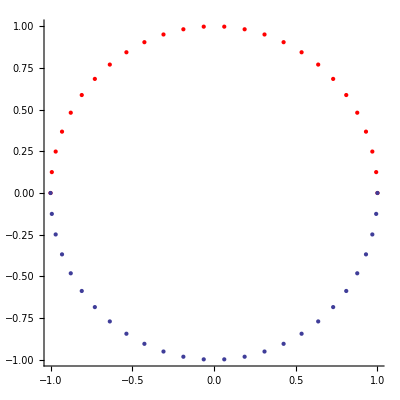

```mathematica
With[{n=25},BRPtsGraph@NestList[Times[{ⅇ^(π ⅈ/n),ⅇ^(-π ⅈ/n)},#]&,{1,1},n]]
```

or equivalently

```mathematica
BRPtsGraph[Table[{ ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{θ,0,π,π/25}]]
```

-Graphics-

Here's another way of doing the graphics -- this one is a bit faster:

```mathematica
BRPtsGraph[lst:{{_?NumericQ,_?NumericQ}..}]:=Module[{lsPairs=cPairsToCoords/@lst},Graphics[{PointSize->Small,Red,Point[lsPairsᵀ⟦1⟧],Blue,Point[lsPairsᵀ⟦2⟧]},Axes->True]]
```

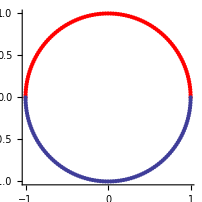

```mathematica
BRPtsGraph[Table[{ ⅇ^(ⅈ θ),ⅇ^(-ⅈ θ)},{θ,0,π,π/100}]]
```

We can include the above function(s) in a more specialised graphics function:

```mathematica
fGraph[{b_,c_},ch_?(MemberQ[{-1,0,1},#]&),n_]:=BRPtsGraph[NestList[f[#,ch]&,N@{b,c},n]⟦3;;⟧]
```

```mathematica
1.4 ⅇ^(-3ⅈ π/4){1,-1}
```

```mathematica
RandomComplex[(1+ⅈ){-1,1},2]
```

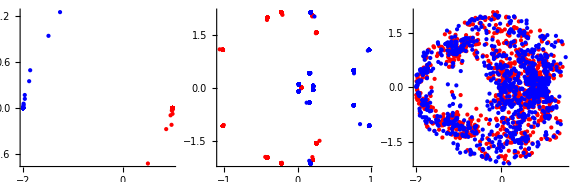
0.244015
-Graphics-

```mathematica
GraphicsRow[fGraph[1.44 ⅇ^(-3ⅈ π/4){1,-1},#,10^3]&/@{1,-1,0},ImageSize->Large]//Timing//TableForm
```

In the f_- graph there is clearly 12 blue points, but only 11 red, this is because the points 0.046±0.0038 ⅈ are hard to distinguish.

To generate the image given in the question, I used the following code:

This method is about two times slower, but it doesn't let the image get dominated by the blue dots...

```mathematica
ComplexToCoords[b_]:={Re[b],Im[b]}
fGraph2[{b_,c_},ch_?(MemberQ[{-1,0,1},#]&),n_]:=Graphics[Join[{PointSize->Small,Red},Riffle[Point/@ComplexToCoords/@Flatten@NestList[f[#,ch]&,N@{b,c},n],{Blue,Red}]],Axes->True]
```

```mathematica
GraphicsRow[fGraph2[{.5,.5},#,10^3]&/@{1,-1,0},ImageSize->Full]//Timing//TableForm
```

```mathematica
Export[NotebookDirectory[]<>"brain.gif",fGraph2[RandomComplex[(1+ⅈ){-1,1},2],0,10^5]]
```

##### v) Cycle

We assume that the iteration converges to the cycle fairly quicky, and then compare the tail elements.  
— we can use Part to extract the tail of a list...  see below.

```mathematica
NestList[f[#,-1]&,{.5,.5},1000]⟦-24;;⟧
```

{{0.206565+2.05067 ⅈ,0.209084-0.0572951 ⅈ},{-0.222954-2.14964 ⅈ,0.0163891+0.0989646 ⅈ},{0.0462693-0.00381433 ⅈ,0.176685+2.15345 ⅈ},{-1.01927+1.08285 ⅈ,0.973002-1.07904 ⅈ},{0.254966-1.57645 ⅈ,0.764305+0.493597 ⅈ},{-0.415649+1.99338 ⅈ,0.160683-0.416927 ⅈ},{0.206565-2.05067 ⅈ,0.209084+0.0572951 ⅈ},{-0.222954+2.14964 ⅈ,0.0163891-0.0989646 ⅈ},{0.0462693+0.00381433 ⅈ,0.176685-2.15345 ⅈ},{-1.01927-1.08285 ⅈ,0.973002+1.07904 ⅈ},{0.254966+1.57645 ⅈ,0.764305-0.493597 ⅈ},{-0.415649-1.99338 ⅈ,0.160683+0.416927 ⅈ},{0.206565+2.05067 ⅈ,0.209084-0.0572951 ⅈ},{-0.222954-2.14964 ⅈ,0.0163891+0.0989646 ⅈ},{0.0462693-0.00381433 ⅈ,0.176685+2.15345 ⅈ},{-1.01927+1.08285 ⅈ,0.973002-1.07904 ⅈ},{0.254966-1.57645 ⅈ,0.764305+0.493597 ⅈ},{-0.415649+1.99338 ⅈ,0.160683-0.416927 ⅈ},{0.206565-2.05067 ⅈ,0.209084+0.0572951 ⅈ},{-0.222954+2.14964 ⅈ,0.0163891-0.0989646 ⅈ},{0.0462693+0.00381433 ⅈ,0.176685-2.15345 ⅈ},{-1.01927-1.08285 ⅈ,0.973002+1.07904 ⅈ},{0.254966+1.57645 ⅈ,0.764305-0.493597 ⅈ},{-0.415649-1.99338 ⅈ,0.160683+0.416927 ⅈ}}

By inspection, we guess that the cycle is of period 12, we check this guess:

```mathematica
NestList[f[#,-1]&,{.5,.5},1000];
%⟦-12;;⟧==%⟦-24;;-13⟧//Chop
```

True

So we have the period 12 cycle displayed below:

```mathematica
NestList[f[#,-1]&,{.5,.5},1000]⟦-12;;⟧//TableForm
```

0.206565+2.05067 ⅈ | 0.209084-0.0572951 ⅈ
-0.222954-2.14964 ⅈ | 0.0163891+0.0989646 ⅈ
0.0462693-0.00381433 ⅈ | 0.176685+2.15345 ⅈ
-1.01927+1.08285 ⅈ | 0.973002-1.07904 ⅈ
0.254966-1.57645 ⅈ | 0.764305+0.493597 ⅈ
-0.415649+1.99338 ⅈ | 0.160683-0.416927 ⅈ
0.206565-2.05067 ⅈ | 0.209084+0.0572951 ⅈ
-0.222954+2.14964 ⅈ | 0.0163891-0.0989646 ⅈ
0.0462693+0.00381433 ⅈ | 0.176685-2.15345 ⅈ
-1.01927-1.08285 ⅈ | 0.973002+1.07904 ⅈ
0.254966+1.57645 ⅈ | 0.764305-0.493597 ⅈ
-0.415649-1.99338 ⅈ | 0.160683+0.416927 ⅈ

Note that the second 6 pts are complex conjugates of the first:

```mathematica
NestList[f[#,-1]&,{.5,.5},1000];
%⟦-12;;-7⟧==%⟦-6;;⟧*//Chop
```

True

Can we find anything interesting about these numbers using some higher precision numerics? -- Not really.

We generate a point on the cycle (up to machine precision)

```mathematica
startPt=Nest[f[#,-1]&,{.5,.5},999]
```

{0.254966+1.57645 ⅈ,0.764305-0.493597 ⅈ}

then find the same point at higher precision

```mathematica
nextPt=Nest[f[SetPrecision[#,10$MachinePrecision],-1]&,startPt,100 12];
```

Let's look at the first half of the cycle (as the rest is the same up to complex conjugation)

```mathematica
TableForm[cycle[-1]=NestList[f[#,-1]&,nextPt,5]]//N[#,10]&
```

0.254966255+1.57644905 ⅈ | 0.764305338-0.493596832 ⅈ
-0.415649097-1.993376349 ⅈ | 0.160682842+0.4169272985 ⅈ
0.206565155+2.05067143 ⅈ | 0.2090839418-0.0572950807 ⅈ
-0.222954208-2.149636065 ⅈ | 0.0163890527+0.09896463567 ⅈ
0.04626926654-0.00381432983 ⅈ | 0.176684941+2.153450395 ⅈ
-1.01927159+1.082852219 ⅈ | 0.973002326-1.079037889 ⅈ

Tried looking up these numbers in the inverse symbolic calculator and online encyclopedia of online sequences —  nothing
Note that they are actually solutions to a large order polynomial

```mathematica
RootApproximant@N[cycle[-1],10]//TableForm
```

Root[2-7 #1-3 #1^2+6 #1^4-4 #1^6-3 #1^7-3 #1^8+6 #1^9-2 #1^10+3 #1^11&,9] | Root[1+#1^3+#1^7+#1^8-#1^10-2 #1^11+#1^12+#1^13-#1^16-#1^17+2 #1^18+3 #1^19-2 #1^20+2 #1^21-2 #1^22+2 #1^23&,18]
(-606309-ⅈ √8454987112295)/1458704 | Root[-1+#1-2 #1^2-2 #1^3+6 #1^4+16 #1^5+21 #1^6-14 #1^7+26 #1^8&,6]
(175367+ⅈ √3030915159893)/848967 | (14961-2 ⅈ √4201986)/71555
(-227189-ⅈ √4798142404131)/1018994 | (23929+ⅈ √20878604479)/1460060
(1288-2 ⅈ √2819)/27837 | (97264+ⅈ √1405319019698)/550494
Root[1-4 #1+6 #1^2-2 #1^3-4 #1^4+8 #1^5-#1^6+3 #1^7-2 #1^8+2 #1^9+#1^11&,3] | Root[3-2 #1^2-#1^3+4 #1^4-#1^5+4 #1^7-6 #1^8+4 #1^9-#1^10+2 #1^11-2 #1^12+#1^13&,12]

```mathematica
RootApproximant@N[cycle[-1],15]//TableForm
```

(140688436+13 ⅈ √4477386322835558)/551792378 | (1136274165-ⅈ √538489458782869803)/1486675689
(-1310360801-ⅈ √39491779728462241535)/3152565016 | (2393204401+ⅈ √38560374264179565503)/14893963614
(67325179+ⅈ √446717605936173443)/325927086 | (258642559-ⅈ √5023348285931535)/1237027372
(-906778321-ⅈ √76436499750703789739)/4067105666 | (39947909+ⅈ √58188941829615827)/2437475166
(17015905-ⅈ √1967711228279)/367758261 | (94527802+ⅈ √1327363257073894307)/535007689
Root[-2+7 #1-7 #1^2+4 #1^3-4 #1^4-4 #1^5-2 #1^6+6 #1^7-#1^8-4 #1^9+4 #1^10+#1^11-4 #1^12-9 #1^13-3 #1^14+#1^16&,4] | Root[5-2 #1+#1^2-8 #1^5+5 #1^6-4 #1^7+2 #1^8+8 #1^9-#1^10-2 #1^12+4 #1^13+5 #1^14-6 #1^15+3 #1^16&,13]

No luck with the polar decomposition either.

```mathematica
Abs[cycle[-1]]//TableForm//N[#,10]&
Arg[cycle[-1]]//TableForm//N[#,10]&
```

1.596934375 | 0.9098354148
2.036249847 | 0.4468191446
2.061048878 | 0.2167921147
2.161167229 | 0.1003125125
0.04642622253 | 2.160686505
1.487105748 | 1.45294745

1.410450284 | -0.5734248004
-1.776365929 | 1.202941128
1.470404461 | -0.2674633328
-1.674143993 | 1.40668066
-0.08225166499 | 1.488932325
2.325957809 | -0.8370254837

##### v) tortoise and hare

We simply translate the question into Mathematica - ie capitalise the functions and add brackets.

```mathematica
findcycle[fn_,x0_]:=Module[{tort,hare,μ=0,λ=1,thecyc},
(* -- 1 -- Find two identical points,  fn^i(x0)=fn^(i+ν)(x0) *)
tort=x0;hare=fn@x0;
While[tort≠hare,tort=fn@tort;hare=fn@fn@hare;μ++];
(* -- 2 -- Find the first time, after μ steps, that that point occurs *)
μ=0;hare=tort;tort=x0;
While[tort≠hare,tort=fn@tort;μ++];
(* -- 3 -- Find minimum length, λ, of cycle 
-- in the process collect the elements in the cycle *)
hare=fn@tort;thecyc={tort};
While[tort≠hare,AppendTo[thecyc,hare];hare=fn@hare;λ++];
(* Output the result  *)
{{μ,λ},thecyc}
]
```

This implementation below has a bit more of an informative exit in the case of a manual abort during the first, cycle finding loop — that code is in brown and can be ignored.  It also has the PrintTemporary commands so that you can see where the algorithm is up to.

```mathematica
findcycle[fn_,x0_]:=Module[{tort,hare,μ=0,λ=1,thecyc},
(* -- Find two identical points,  fn^i(x0)=fn^(i+ν)(x0) -- *)
Catch[
tort=x0;hare=fn@x0;
CheckAbort[
While[tort≠hare,tort=fn@tort;hare=fn@fn@hare;μ++];,
Print["Calculation was aborted, returning current values and number of steps: {tort,hare,steps}"];
Throw[{tort,hare,μ}]];PrintTemporary[{tort}];
(* -- Find the first time, after μ steps, that that point occurs --*)
μ=0;hare=tort;tort=x0;
While[tort≠hare,tort=fn@tort;μ++];PrintTemporary[μ];
(* -- Find minimum length, λ, of cycle -- *)
hare=fn@tort;thecyc={tort};
While[tort≠hare,AppendTo[thecyc,hare];hare=fn@hare;λ++];
(* Output the result  *)
{{μ,λ},thecyc}
]]
```

We check it on the two cases that we already know:

```mathematica
findcycle[f[#,1]&,{.5,.5}]
```

{{1294,1},{{1.+0. ⅈ,-2.+0. ⅈ}}}

```mathematica
findcycle[f[#,-1]&,{.5,.5}]
```

{{143,12},{{0.206565-2.05067 ⅈ,0.209084+0.0572951 ⅈ},{-0.222954+2.14964 ⅈ,0.0163891-0.0989646 ⅈ},{0.0462693+0.00381433 ⅈ,0.176685-2.15345 ⅈ},{-1.01927-1.08285 ⅈ,0.973002+1.07904 ⅈ},{0.254966+1.57645 ⅈ,0.764305-0.493597 ⅈ},{-0.415649-1.99338 ⅈ,0.160683+0.416927 ⅈ},{0.206565+2.05067 ⅈ,0.209084-0.0572951 ⅈ},{-0.222954-2.14964 ⅈ,0.0163891+0.0989646 ⅈ},{0.0462693-0.00381433 ⅈ,0.176685+2.15345 ⅈ},{-1.01927+1.08285 ⅈ,0.973002-1.07904 ⅈ},{0.254966-1.57645 ⅈ,0.764305+0.493597 ⅈ},{-0.415649+1.99338 ⅈ,0.160683-0.416927 ⅈ}}}

Finally we find the new case that was asked for:

```mathematica
findcycle[f[f[f[#,1],1],-1]&,{.5,.5}]
```

{{27,4},{{-1.24599+0.84868 ⅈ,1.19089-0.561702 ⅈ},{-1.38743-1.04031 ⅈ,0.96014+0.254937 ⅈ},{-1.24599-0.84868 ⅈ,1.19089+0.561702 ⅈ},{-1.38743+1.04031 ⅈ,0.96014-0.254937 ⅈ}}}

##### Below you'll find a little exrtra playing around that was not part of the exam.

##### More complicated combinations: f[{b,c},{±1,±1,±1,±1,…}]

The next simplest case is (1,-1):

```mathematica
findcycle[f[f[#,1],-1]&,{.25,.5}]//Chop
```

{{32,1},{{-0.272304-1.79878 ⅈ,0}}}

a fixed point????
Let's check...

```mathematica
f[f[{b,0},1],-1]//FullSimplify
```

{1/4 (b-√(b^2)-√2 √(4 √(b^2)+b (4+b-√(b^2)))),1/4 (b-√(b^2)+√2 √(4 √(b^2)+b (4+b-√(b^2))))}

```mathematica
Reduce[f[f[{b,0},1],-1]=={b,0}∧Re[b]≥0]
```

Im[b]≤0&&Re[b]==0

```mathematica
Reduce[f[f[{b,0},1],-1]=={b,0}∧Re[b]<0]
```

Re[b]<0

So any (a,0) with Re(a)<0 or Re(a)==0 and Im(a)≤0 is a fixed point!
This is illustrated below.

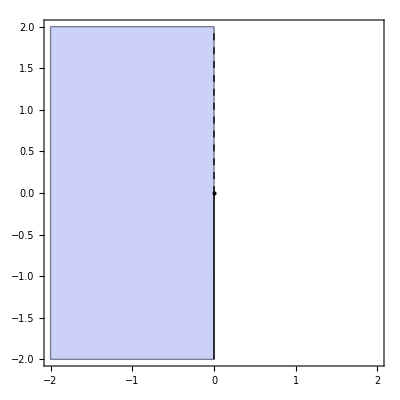

```mathematica
RegionPlot[x<0∨x==0∧y≤0,{x,-2,2},{y,-2,2},Epilog->{Line[{{0,-2},{0,0}}],Point[{0,0}],Dashed,Line[{{0,0},{0,2}}]}]
```

Order 3 maps? - only (1,1,-1) and (1,-1,-1) are new.

We have a 4-cycle  (or another 12-cycle depending on how you count...)

```mathematica
findcycle[f[f[f[#,1],1],-1]&,{.5,.5}]//Chop//TableForm
```

27 | 4 |  | 
-1.24599+0.84868 ⅈ
1.19089-0.561702 ⅈ | -1.38743-1.04031 ⅈ
0.96014+0.254937 ⅈ | -1.24599-0.84868 ⅈ
1.19089+0.561702 ⅈ | -1.38743+1.04031 ⅈ
0.96014-0.254937 ⅈ

```mathematica
findcycle[f[#,{1,1,-1}]&,{.5,.5}]//Chop//TableForm
```

31 | 4 |  | 
0.952033-1.42358 ⅈ | 0.4354+0.383276 ⅈ
0.0550998-0.286978 ⅈ | -1.00713+1.71056 ⅈ
-1.24599+0.84868 ⅈ | 1.19089-0.561702 ⅈ | 0.639626+0.567178 ⅈ | 0.606365-1.41586 ⅈ
0.427292+0.78537 ⅈ | -1.06692-1.35255 ⅈ
-1.38743-1.04031 ⅈ | 0.96014+0.254937 ⅈ | 0.952033+1.42358 ⅈ | 0.4354-0.383276 ⅈ
0.0550998+0.286978 ⅈ | -1.00713-1.71056 ⅈ
-1.24599-0.84868 ⅈ | 1.19089+0.561702 ⅈ | 0.639626-0.567178 ⅈ | 0.606365+1.41586 ⅈ
0.427292-0.78537 ⅈ | -1.06692+1.35255 ⅈ
-1.38743+1.04031 ⅈ | 0.96014-0.254937 ⅈ

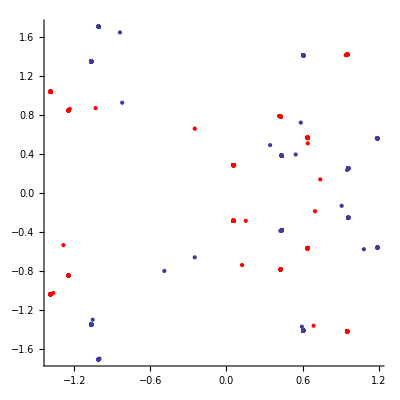

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,1,-1}]&,{.5,.5},200],1]]
```

Next!!  We have a 2-cycle  (or another 6-cycle depending on how you count...)

```mathematica
findcycle[f[f[f[#,1],-1],-1]&,{.5,.5}]//Chop//TableForm
```

37 | 2
0.338204-0.313006 ⅈ
1.00885+1.58785 ⅈ | 0.338204+0.313006 ⅈ
1.00885-1.58785 ⅈ

```mathematica
findcycle[f[#,{1,-1,-1}]&,{.5,.5}]//Chop//TableForm
```

37 | 2
0.508848+1.05361 ⅈ | -0.847052-1.36661 ⅈ
-1.34705-1.27485 ⅈ | 0.838204+0.221244 ⅈ
0.338204-0.313006 ⅈ | 1.00885+1.58785 ⅈ | 0.508848-1.05361 ⅈ | -0.847052+1.36661 ⅈ
-1.34705+1.27485 ⅈ | 0.838204-0.221244 ⅈ
0.338204+0.313006 ⅈ | 1.00885-1.58785 ⅈ

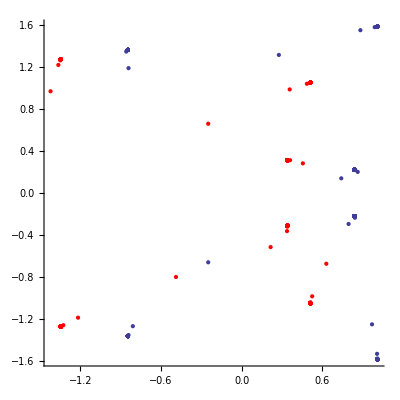

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,-1,-1}]&,{.5,.5},200],1]]
```

Order 4 maps? - only (1,1,1,-1), (1,1,-1,-1) and (1,-1,-1,-1) are new.

A 2-cycle / 8-cycle

```mathematica
findcycle[f[f[f[f[#,1],-1],-1],-1]&,{.5,.5}]//Chop//TableForm
```

29 | 2
-0.412248+1.90006 ⅈ
0.124711-0.43208 ⅈ | -0.412248-1.90006 ⅈ
0.124711+0.43208 ⅈ

```mathematica
findcycle[f[#,{1,-1,-1,-1}]&,{.5,.5}]//Chop//TableForm
```

31 | 2
0.226492-0.0425403 ⅈ | 0.185757+1.9426 ⅈ
-1.0571+1.0529 ⅈ | 0.830612-1.01036 ⅈ
0.287537-1.46798 ⅈ | 0.769567+0.415083 ⅈ
-0.412248+1.90006 ⅈ | 0.124711-0.43208 ⅈ | 0.226492+0.0425403 ⅈ | 0.185757-1.9426 ⅈ
-1.0571-1.0529 ⅈ | 0.830612+1.01036 ⅈ
0.287537+1.46798 ⅈ | 0.769567-0.415083 ⅈ
-0.412248-1.90006 ⅈ | 0.124711+0.43208 ⅈ

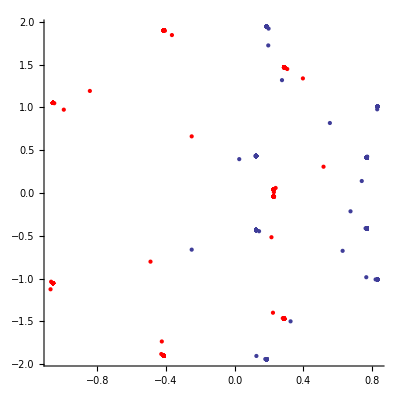

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,-1,-1,-1}]&,{.5,.5},200],1]]
```

6- or 24-cycle

```mathematica
findcycle[f[f[f[f[#,1],1],-1],-1]&,{.5,.5}]//Chop//TableForm
```

41 | 6 |  |  |  | 
0.739244-0.54466 ⅈ
0.834491+0.0683941 ⅈ | 0.551798+0.035166 ⅈ
1.07076-0.663738 ⅈ | 0.777189+0.741312 ⅈ
0.790478-0.159801 ⅈ | 0.504898-0.0590164 ⅈ
1.19531+0.707566 ⅈ | 0.779645+0.162878 ⅈ
0.805581-0.780689 ⅈ | 0.783786-0.0566728 ⅈ
0.873002+0.536678 ⅈ

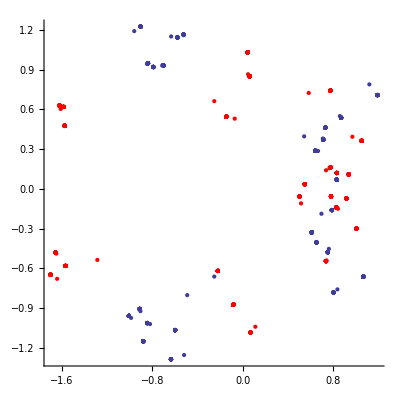

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,1,-1,-1}]&,{.5,.5},200],1]]
```

Looks like a 2-cycle...

```mathematica
findcycle[f[f[f[f[#,1],1],1],-1]&,{.5,.5}]//Chop//TableForm
```

Calculation was aborted, returning current values and number of steps: {tort,hare,steps}

-1.5352+0.283087 ⅈ | 0.535199-0.283088 ⅈ
-1.5352+0.283088 ⅈ | 0.535199-0.283088 ⅈ
2694725 |

Converges too slowly for our algorithm...  but it's good enough for me.

```mathematica
f[f[f[f[#,1],1],1],-1]&@{-1.535199826805798+0.2830871834678583ⅈ,0.5351988154526185-0.2830876544707477ⅈ}
f[f[f[f[#,1],1],1],-1]&@%
```

{-1.5352-0.283087 ⅈ,0.535199+0.283088 ⅈ}

{-1.5352+0.283087 ⅈ,0.535199-0.283088 ⅈ}

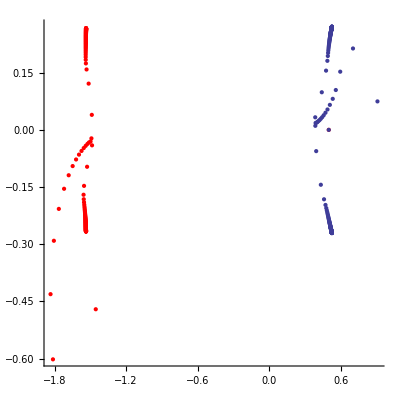

```mathematica
BRPtsGraph[NestList[f[f[f[f[#,1],1],1],-1]&,{.5,.5},200]]
```

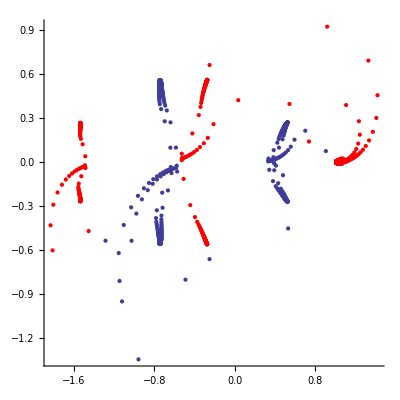

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,1,1,-1}]&,{.5,.5},200],1]]
```

Order 5 maps?

```mathematica
findcycle[f[#,{1,1,1,1,-1}]&,{.5,.5}]//Chop//TableForm
```

21 | 2
0.809855+1.08215 ⅈ | -0.995195-1.10586 ⅈ
-1.55317-1.21343 ⅈ | 0.743315+0.13128 ⅈ
0.302849-0.249299 ⅈ | 1.25032+1.46273 ⅈ
-0.745344+1.38785 ⅈ | 0.442495-1.13855 ⅈ
0.043954-1.63901 ⅈ | 0.70139+0.251167 ⅈ | 0.0999334-0.358356 ⅈ | -0.143887+1.99737 ⅈ
-1.08263+1.15494 ⅈ | 0.982698-0.796587 ⅈ
0.456885-1.5925 ⅈ | 0.625746+0.437554 ⅈ
-0.576077+1.94882 ⅈ | 0.119192-0.356323 ⅈ
0.18534+0.0237122 ⅈ | 0.390738-1.97253 ⅈ

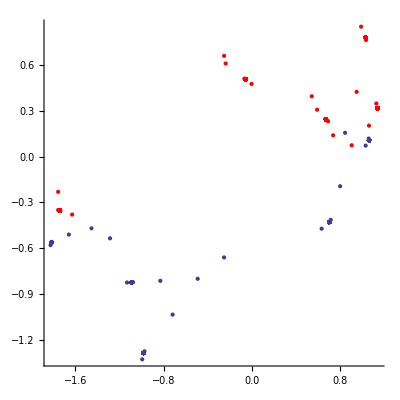

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,1,1,1,-1}]&,{.5,.5},200],1]]
```

Order 6 maps?

```mathematica
findcycle[f[#,{1,1,1,1,1,-1}]&,{.5,.5}]//Chop//TableForm
```

Calculation was aborted, returning current values and number of steps: {tort,hare,steps}

1.00006-2.89451×10^-6 ⅈ
0.829316-0.144759 ⅈ | -0.405655+0.766939 ⅈ
-0.594402-0.766937 ⅈ | 1.00003-0.0000153858 ⅈ
-0.594374-0.766924 ⅈ | 0.496246+0.384905 ⅈ
-1.49627-0.38489 ⅈ | 1.00001-7.72253×10^-6 ⅈ
-1.49626-0.384898 ⅈ | -1.82937-0.144762 ⅈ
0.829363+0.14477 ⅈ
1.00003+1.45332×10^-6 ⅈ
0.829344+0.144769 ⅈ | -0.405637-0.766967 ⅈ
-0.594392+0.766965 ⅈ | 1.00001+7.69883×10^-6 ⅈ
-0.594377+0.766959 ⅈ | 0.496258-0.384919 ⅈ
-1.49627+0.384911 ⅈ | 1.00001+3.86384×10^-6 ⅈ
-1.49626+0.384915 ⅈ | -1.82937+0.144771 ⅈ
0.829368-0.144775 ⅈ
9601 |  |  |  |  |

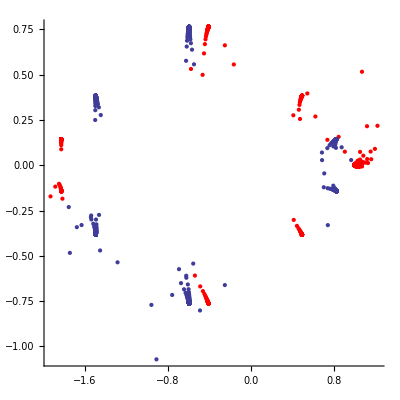

```mathematica
BRPtsGraph[Flatten[Rest@NestList[f[#,{1,1,1,1,1,-1}]&,{.5,.5},200],1]]
```

##### g∘f_±==id

```mathematica
g[{x1_,x2_}]:={-x1-x2,x1 x2}
```

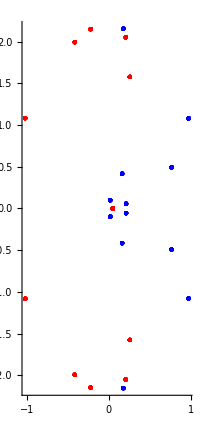

```mathematica
NestList[g,nextPt,400];
BRPtsGraph[%]
```

```mathematica
Nest[g,{x,y},1]//Expand
Reduce[%=={x,y}]
```

{-x-y,x y}

(y==-2&&x==1)||(y==0&&x==0)

```mathematica
Nest[g,{x,y},2]//Expand
Reduce[%=={x,y}]
```

{x+y-x y,-x^2 y-x y^2}

(y==-2&&x==1)||y==0

```mathematica
Nest[g,{x,y},3]//Expand
Reduce[%=={x,y}]
```

{-x-y+x y+x^2 y+x y^2,-x^3 y-2 x^2 y^2+x^3 y^2-x y^3+x^2 y^3}

(y==0&&x==0)||((y==-2||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,1]||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,2]||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,3]||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,4]||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,5]||y==Root[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&,6])&&x==1/14 (38-44 y-2 y^2+3 y^3+3 y^4+2 y^5-y^6))

```mathematica
Factor[4-12 #1+16 #1^2-10 #1^3+4 #1^4-2 #1^5+#1^6&[y],Extension->{ⅈ,√3}]
```

(-ⅈ+√3-2 √3 y+(ⅈ+√3) y^2-ⅈ y^3) (ⅈ+√3-2 √3 y+(-ⅈ+√3) y^2+ⅈ y^3)

```mathematica
Nest[g,{x,y},4]//Expand
Reduce[%=={x,y}]
```

{x+y-x y-x^2 y+x^3 y-x y^2+2 x^2 y^2-x^3 y^2+x y^3-x^2 y^3,x^4 y+3 x^3 y^2-2 x^4 y^2-x^5 y^2+3 x^2 y^3-4 x^3 y^3-2 x^4 y^3+x^5 y^3+x y^4-2 x^2 y^4-2 x^3 y^4+2 x^4 y^4-x^2 y^5+x^3 y^5}

(y==0&&(x==-1||x==1))||((y==-2||y==0)&&x==1)||y==0

```mathematica
Nest[g,{x,y},5]//Expand
Reduce[%=={x,y}]
```

{-x-y+x y+x^2 y-x^3 y-x^4 y+x y^2-2 x^2 y^2-2 x^3 y^2+2 x^4 y^2+x^5 y^2-x y^3-2 x^2 y^3+4 x^3 y^3+2 x^4 y^3-x^5 y^3-x y^4+2 x^2 y^4+2 x^3 y^4-2 x^4 y^4+x^2 y^5-x^3 y^5,x^5 y+4 x^4 y^2-3 x^5 y^2-2 x^6 y^2+x^7 y^2+6 x^3 y^3-9 x^4 y^3-5 x^5 y^3+9 x^6 y^3-2 x^7 y^3-x^8 y^3+4 x^2 y^4-9 x^3 y^4-6 x^4 y^4+21 x^5 y^4-10 x^6 y^4-3 x^7 y^4+2 x^8 y^4+x y^5-3 x^2 y^5-5 x^3 y^5+21 x^4 y^5-16 x^5 y^5-4 x^6 y^5+7 x^7 y^5-x^8 y^5-2 x^2 y^6+9 x^3 y^6-10 x^4 y^6-4 x^5 y^6+10 x^6 y^6-3 x^7 y^6+x^2 y^7-2 x^3 y^7-3 x^4 y^7+7 x^5 y^7-3 x^6 y^7-x^3 y^8+2 x^4 y^8-x^5 y^8}

(y==0&&x==0)||((y==-2||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,1]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,2]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,3]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,4]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,5]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,6]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,7]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,8]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,9]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,10]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,11]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,12]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,13]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,14]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,15]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,16]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,17]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,18]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,19]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,20]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,21]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,22]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,23]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,24]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,25]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,26]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,27]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,28]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,29]||y==Root[16-272 #1+2032 #1^2-9072 #1^3+27680 #1^4-60616 #1^5+96592 #1^6-112288 #1^7+96416 #1^8-66504 #1^9+48352 #1^10-45520 #1^11+42420 #1^12-30296 #1^13+16116 #1^14-8272 #1^15+5822 #1^16-4172 #1^17+2250 #1^18-890 #1^19+269 #1^20-134 #1^21+133 #1^22-78 #1^23+12 #1^24+#1^25+7 #1^26-6 #1^27+4 #1^28-2 #1^29+#1^30&,30])&&x==(88217332394811426665550601182412229918390901880432-1047734072468571624017637903968738797603878902140592 y+5569541807826554465520698967378645613968859978568640 y^2-18543567871478182665743530685253232839752178752210624 y^3+41999039904799616806375272617431806799673657719371152 y^4-65194769466402485205500730251900156869767818042646248 y^5+67605538155965772944549877652608491904812599948439064 y^6-44446118836998289238756408494293061072473878239567080 y^7+19003293791725646969137041090465244661682329510618024 y^8-13529189031932274140131655192582429605924243795707080 y^9+21094939286068541376357385110465146325442177347439356 y^10-21436650134843172198023647232124394806726022772673772 y^11+10703099985521259025590995901622582831605596372838100 y^12-1162280051297260555426002592367013260831583552474948 y^13-116648845447758462332887161339804996186288981777592 y^14-1721136214902676500488507636934671700401753322386538 y^15+1467767875480852614080442945585989861776579653225170 y^16-249841599332816633014821232093681541192540644227686 y^17-238919915404259727170592007959672664431953224157676 y^18+209459293596575771794823723098346998613476955077762 y^19-16874238360367805810958842003571746265922606304701 y^20-76064241072609559782485728434557815834784267072436 y^21+20002723623482171134228916760355517095564183603267 y^22+30344499385731679844116031870694028943688083091796 y^23-10283295958489619963265452732210227059199871423314 y^24-8500644089059805626399804706244360380784896288819 y^25+2719988967122706024370682611918590937016556463933 y^26-1219700635804513277286294486028968084704877293546 y^27-21592572645182176829044795688800545731346434914 y^28-124472178792907846901370119825684992286208384622 y^29-601386623615309155572642540357926252371704860993 y^30)/1942471905562552916725387540235184116395325870288)

## Section. Evolving polygon [20 Marks]

There are many examples in physics and engineering where the dynamics of some system is influenced by, even defined by, its geometry.

The geometric property of curvature is, for some systems, a factor in determining how the system evolves.
Real examples include (i) anything with surface tension effects and (ii) general relativity.

The example which follows has been selected not because of any applications but because it can use the methods treated in MATH2200.

The dynamics we're interested in is based on a cyclic matrix: the first part of this question is about this matrix.

Here is some code that will generate such a matrix given a vector,

```mathematica
CyclicMatrix[v_List]:=NestList[RotateRight,v,Length[v]-1]
```

Let's define the cyclic matrix A(n) by

```mathematica
A[n_Integer?(#>2&)]:=CyclicMatrix[RotateLeft[PadRight[{-1,2,-1},n],1]]
```

```mathematica
MatrixForm/@(A/@Range[3,7,2])
```

{(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2),(2 | -1 | 0 | 0 | -1
-1 | 2 | -1 | 0 | 0
0 | -1 | 2 | -1 | 0
0 | 0 | -1 | 2 | -1
-1 | 0 | 0 | -1 | 2),(2 | -1 | 0 | 0 | 0 | 0 | -1
-1 | 2 | -1 | 0 | 0 | 0 | 0
0 | -1 | 2 | -1 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1 | 0 | 0
0 | 0 | 0 | -1 | 2 | -1 | 0
0 | 0 | 0 | 0 | -1 | 2 | -1
-1 | 0 | 0 | 0 | 0 | -1 | 2)}

Question SectionExercise)  [4 Marks]

Show that, for general integer n>2, the nullspace of A(n) is non-trivial.

Using Mathematica show that, for each of n=4, n=5 and n=6, the nullspace of A(n) is one-dimensional.

Write some text which establishes that, for general positive integer n, the nullspace of A(n) is one-dimensional.

Solution

i.

The key observation is that dotting any vector v with the vector (1,1,1,…) just yields the sum of all the elements in v.  Each row in A(n) has the sum -1+2-1+0+…+0=0 , thus the vector (1,1,1…) is always in the nullspace of A(n), thus the nullspace is nontrivial.

A check:

```mathematica
onesVec[n_]:=ConstantArray[1,n]
```

```mathematica
And@@Table[A[n].onesVec[n]==0 onesVec[n],{n,3,100}]
```

True

An alternate solution is to calculate the determinant.  If it's zero then there must be a zero eigenvector, thus the nullspace is nontrivial.

Once again, if you add up any row, the total is zero.  Let's define a matrix 𝟙_UD(n)=(1 | 1 | ⋯ | 1
0 | 1 | ⋯ | 1
⋮ | ⋱ | ⋱ | ⋮
0 | ⋯ | 0 | 1) which is zero below the diagonal and one everywhere else.  When acting on the left to a matrix, it has the affect of adding to any matrix element all the elements directly below it.  This means that it will make the first row of A(n) zero.  Then we have 0=Det[𝟙_UD·A(n)]=Det[𝟙_UD]Det[A(n)]=1Det[A(n)]=Det[A], which is our result.

A check using Mathematica:

```mathematica
Subscript[𝟙, UD][n_]:=SparseArray[{{i_,j_}/;j≥i->1},{n,n}]
MatrixForm/@Table[Subscript[𝟙, UD][n],{n,3,5}]
And@@Table[Det[Subscript[𝟙, UD][n]]==1,{n,1,100}]
```

{(1 | 1 | 1
0 | 1 | 1
0 | 0 | 1),(1 | 1 | 1 | 1
0 | 1 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1),(1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)}

True

```mathematica
MatrixForm/@Table[Subscript[𝟙, UD][n].A[n],{n,3,9,2}]
```

{(0 | 0 | 0
-2 | 1 | 1
-1 | -1 | 2),(0 | 0 | 0 | 0 | 0
-2 | 1 | 0 | 0 | 1
-1 | -1 | 1 | 0 | 1
-1 | 0 | -1 | 1 | 1
-1 | 0 | 0 | -1 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 1 | 0 | 0 | 0 | 0 | 1
-1 | -1 | 1 | 0 | 0 | 0 | 1
-1 | 0 | -1 | 1 | 0 | 0 | 1
-1 | 0 | 0 | -1 | 1 | 0 | 1
-1 | 0 | 0 | 0 | -1 | 1 | 1
-1 | 0 | 0 | 0 | 0 | -1 | 2),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2)}

```mathematica
And@@Table[Det[Subscript[𝟙, UD][n].A[n]]==Det[A[n]]==0,{n,3,100}]
```

True

ii.

```mathematica
Table[NullSpace[A[n]],{n,4,6}]
```

{{{1,1,1,1}},{{1,1,1,1,1}},{{1,1,1,1,1,1}}}

iii.

The principal submatrix (first (n-1) rows and (n-1) columns) for A(n) is the (n-1)×(n-1) tridiagonal matrix T(n-1).  The matrix T(n) has 2's down its diagonal and -1's on its super- and sub-diagonals.

The matrix T(n) is nonsingular, the easiest way to see this is to note that its determinant satisfies the recurrence Det[T(n)]=2Det[T(n-1)]-Det[T(n-2)] with the initial conditions Det[T(1)]=2 and Det[T(2)]=3.  This has the solution Det[T(n)]=n+1.

```mathematica
RSolve[{Subscript[T, n]==2 Subscript[T, n-1]-Subscript[T, n-2],Subscript[T, 2]==3,Subscript[T, 1]==2},Subscript[T, n],n]
T[n_Integer]:=SparseArray[{{i_,i_}->2,{i_,j_}/;Abs[i-j]==1->-1},{n,n}]
And@@(Det[T[#]]==#+1&/@Range[100])
```

{{T_n→1+n}}

True

Than T(n) is nonsingular implies that Rank(A(n))≥n-1.
The nontrivial nullspace of A(n) implies that Nullity(A(n))≥1.
But, the Rank-Nullity theorem from 1st year, tells us that Rank(A(n))+Nullity(A(n))==n,
thus we must have Nullity(A(n))==1,  as we are required to show.

Consider a list of n points in the complex plane, {z_1,z_2,…,z_n}.  By cyclicly joining the points we construct an n-sided polygon.
Specify an inward pointing direction at a vertex z_j to be

N_j==(z_(j+1)-z_j)-(z_j-z_(j-1))

where the indices j are cyclic (ie j+n=j).

Now consider the vertices as functions of time, z_j=z_j(t), which evolve in the directions N_j:

(ⅆ z_j)/ⅆt==N_j==(z_(j+1)-z_j)-(z_j-z_(j-1))

By writing z⃗==(z_1,z_2,…,z_n)ᵀ and using A(n) is as above, we can write this as the matrix equation

(ⅆ z⃗)/ⅆt+A(n)·z⃗==0 .

What can be shown is that pretty well any randomly chosen initial polygon evolves towards an ‘affinely regular polygon’, e.g. any randomly chosen initial quadrilateral evolves towards a parallelogram.

By summing the equations we can see that the vertex sum, ∑z_j, stays constant.  So without loss of generality, we can take the initial vertices so to be centered around zero.

Here is some code that you can use to plot any polygon given as a list of complex numbers.

```mathematica
showNgon[lst_]:=ListPlot[{Re[#],Im[#]}&/@Append[lst,First@lst],
PlotStyle->PointSize[Large],Joined->True,Mesh->All,AxesOrigin->{0,0},PlotRange->1.1Max[Abs/@lst]{{-1,1},{-1,1}}]
```

Let's plot a random quadrilateral:  (it might be a crossed quadrilateral, but that is not important)

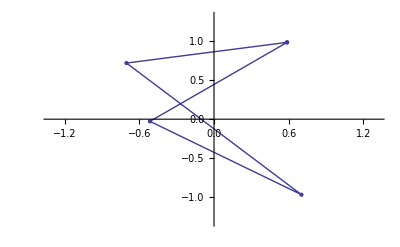

```mathematica
showNgon[RandomComplex[{-1-ⅈ,1+ⅈ},4]]
```

To make a quadrilateral centered at (0,0) we can use the vertices (#1-Mean[#1]&)[RandomComplex[{-1-ⅈ,1+ⅈ},4]].

Question SectionExercise)  [4 Marks]

Have Mathematica find the eigenvalues and eigenvectors of A(4) and find the matrix exponential of (-t A(4)).

Use a Mathematica manipulate command to plot the evolution in time of an initally random quadrilateral under the above system DEs.

Solution

i.

```mathematica
Eigensystem[-A[4]]
```

{{-4,-2,-2,0},{{-1,1,-1,1},{0,-1,0,1},{-1,0,1,0},{1,1,1,1}}}

```mathematica
MatrixExp[-t A[4]]//Simplify//MatrixForm
```

(1/4 ⅇ^(-4 t) (1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (-1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4
1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (-1+ⅇ^(2 t))^2
1/4 ⅇ^(-4 t) (-1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4
1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (-1+ⅇ^(2 t))^2 | 1/4-ⅇ^(-4 t)/4 | 1/4 ⅇ^(-4 t) (1+ⅇ^(2 t))^2)

Taking a common factor of ⅇ^(-2t) out of the matrix exponential is revealing:

```mathematica
ⅇ^(2 t)MatrixExp[-t A[4]]//FullSimplify//MatrixForm
```

(Cosh[t]^2 | Cosh[t] Sinh[t] | Sinh[t]^2 | Cosh[t] Sinh[t]
Cosh[t] Sinh[t] | Cosh[t]^2 | Cosh[t] Sinh[t] | Sinh[t]^2
Sinh[t]^2 | Cosh[t] Sinh[t] | Cosh[t]^2 | Cosh[t] Sinh[t]
Cosh[t] Sinh[t] | Sinh[t]^2 | Cosh[t] Sinh[t] | Cosh[t]^2)

ii.

The solution to the DE is z⃗(t)=ⅇ^-tA z⃗(0)... let's plot it in Mathematica:

```mathematica
evMat[t_]=MatrixExp[-t A[4]];
```

```mathematica
With[{z=(#1-Mean[#1]&)[RandomComplex[{-1-ⅈ,1+ⅈ},4]]},
Manipulate[showNgon[evMat[t].z],{t,0,4,Animator}]]
```

In the below, we rescale the vertices as we go — (the choice of rescaling is particular to the quadrilateral)

```mathematica
With[{z=(#1-Mean[#1]&)[RandomComplex[{-1-ⅈ,1+ⅈ},4]]},
Manipulate[showNgon[ⅇ^(2t) evMat[t].z],{t,0,4,Animator}]]
```

The shapes, at large time are in general ‘affinely regular polygons’.  When n=4, these are parallelograms. Continuing with our normalisation convention of ∑z_i=0, a parallelogram is defined by two vertices z_1 and z_2 with the 3^rd and 4^th vertices are -z_1 and -z_2 respectively.

After a time t, our intial parallelogram has evolved to z⃗(t)=ⅇ^(-t A)·(z_1,z_2,-z_1,-z_2)ᵀ

Question SectionExercise)  [3 Marks]

Show that under the DE (DisplayFormulaNumbered), parallelograms evolve as parallelograms.

Solution

Here's a check that we really are working with parallelograms:

```mathematica
Manipulate[showNgon[{x.{1,ⅈ},y.{1,ⅈ},-x.{1,ⅈ},-y.{1,ⅈ}}],
{{x,{.5,0}},Locator},{{y,{0,.5}},Locator}]
```

Now, here's how a parallelogram evolves in time:

```mathematica
z[t]=MatrixExp[-t A[4]].{z1,z2,-z1,-z2};
```

To check that it remains a parallelogram (which is all that the question is asking), we simply investigate the ratios

```mathematica
z[t]⟦1⟧/z[t]⟦3⟧//Simplify
z[t]⟦2⟧/z[t]⟦4⟧//Simplify
```

-1

-1

```mathematica
Clear[z]
```

Given the n points in the plane, z⃗=(z_1,z_2,…,z_n)ᵀ, there is (up to multiplication by a constant) a unique n-th degree polynomial with these points as its zeros.

p_(z⃗)(w)==(w-z_1)⋯(w-z_n) .

Question SectionExercise)  [3 Marks]

Given the polynomial from a parallelogram,

```mathematica
Subscript[pp, {z1_,z2_}][w_]:=(w-z1)(w-z2)(w+z1)(w+z2)
```

show that the zeros of its derivative (with respect to w) lie on a straight line.

Solution

```mathematica
Factor[D[Subscript[pp, {Subscript[z, 1],Subscript[z, 2]}][w], w]]
Solve[%==0,w]
```

2 w (2 w^2-z_1^2-z_2^2)

{{w→0},{w→-(√(z_1^2+z_2^2))/(√2)},{w→(√(z_1^2+z_2^2))/(√2)}}

The above points are all real multiples of the (complex) number √(z_1^2+z_2^2) and thus lie on a straight line.

Here is a graphical demonstration:

```mathematica
dP[z1_,z2_]:={Re[#],Im[#]}&/@((z1^2+z2^2)^(1/2)/2{-1,0,1})
With[{z1=x.{1,ⅈ},z2=y.{1,ⅈ}},Manipulate[
Show[showNgon[{z1,z2,-z1,-z2}],Graphics[{Red,PointSize->Large,Point[dP[z1,z2]]}]],
{{x,{.8,.8}},Locator},{{y,{0,.5}},Locator}]]
```

Question SectionExercise)  [3 Marks]

As in Exercise 2b, use a Mathematica Manipulate command to plot the evolution in time t , according to our system of d.e.s, of the quadrilateral formed by the evolution a random quadrilateral, shown in blue.
Within the manipulate also show, in red, the zeros of the derivative of the polynomial whose zeros are the vertices of the evolving quadrilateral.

(Remark. You should see the 3 red points evolving towards a straight line.)

Solution

See the solution to 2f) below.

Question SectionExercise)  [3 Marks]

As in Question 2e), use a Mathematica Manipulate command to plot the evolution in time t , according to our system of d.e.s, of the hexagon formed by the evolution a random initial hexagon, shown in blue.
Within the manipulate also show, in red, the zeros of the derivative of the polynomial whose zeros are the vertices of the evolving hexagon.

(Remark. You should see the 5 red points evolving towards a straight line.)

Solution

Here's a completely general manipulate:  just set n=…

```mathematica
Module[{z0,z,dz,w,max,n=17},
z0=# Max[Abs/@#]^-1&[#-Mean[#]]&@RandomComplex[{-1-ⅈ,1+ⅈ},n];
z=MatrixExp[-# A[n]].z0&;
dz={Re[#],Im[#]}&/@(w/.NSolve[D[Times@@(w-z[#]), w]==0])&;
Manipulate[Show[showNgon[z[t]],Graphics[{Red,PointSize->Large,Point[dz[t]]}],AxesOrigin->{0,0},Ticks->False,PlotRange->All,PlotLabel->Row[{
"t=",NumberForm[t,{IntegerLength[n],3}],"  —  ",
"x-scale≃",ScientificForm[Max[Abs/@Re/@z[t]],1],"  —  ",
"y-scale≃",ScientificForm[Max[Abs/@Im/@z[t]],1]}]],
{t,0,n,Animator}]]
```

### An aside

For the quadrilateral, we used a rescaling z(t)→ⅇ^(2t)z(t).
For the hexagon, a suitable rescaling is z(t)→ⅇ^t z(t).

These can both be viewed as redefinitions of A(n);    A(n)→A(n)-c_n ℐ_n
where ℐ_n is the n×n identity matrix and c_4=2, c_6=1.   Can this be generalised?

Let's examine the behaviour of a regular polygon under the DEs

```mathematica
regPolygon[n_]:=Exp[2π ⅈ #/n]&/@Range[0,n-1]
```

```mathematica
Manipulate[Show[showNgon[regPolygon[n]],AspectRatio->1],{{n,5},Range[3,20]}]
```

The regular n-gon is an eigenvector of A(n):

```mathematica
c/.First@Solve[A[#].regPolygon[#]==c regPolygon[#],c]&/@Range[3,10]//FullSimplify
%//N//Chop
```

{3,2,1/2 (5-√5),1,2-(-1)^(2/7)+(-1)^(5/7),2-√2,2-(-1)^(2/9)+(-1)^(7/9),1/2 (3-√5)}

{3.,2.,1.38197,1.,0.75302,0.585786,0.467911,0.381966}

By subtracting out the constant scalar matrix with the above value from A(n), we can make the regular polygons stable under the DE.

But first, we need the general form of the eigenvalue — I can't be bothered proving it's correct, so here's my guess:

```mathematica
c[n_]:=2-(-1)^(2/n)+(-1)^((n-2)/n)
```

```mathematica
And@@(Table[A[n].regPolygon[n]==c[n]regPolygon[n],{n,3,50}]//Simplify)
```

True

So here's the previous manipulate, with the scaling shifted to the DE, not the picture:

```mathematica
Module[{z0,z,dz,w,max,n=7},
z0=# Max[Abs/@#]^-1&[#-Mean[#]]&@RandomComplex[{-1-ⅈ,1+ⅈ},n];
z=MatrixExp[-# (A[n]-IdentityMatrix[n]c[n])].z0&;
dz={Re[#],Im[#]}&/@(w/.NSolve[D[Times@@(w-z[#]), w]==0])&;
Manipulate[Show[showNgon[z[t]],Graphics[{Red,PointSize->Large,Point[dz[t]]}],AxesOrigin->{0,0},PlotRange->All,PlotLabel->Row[{"t=",t}]],
{t,0,n,Animator}]]
```

## Section. Nonlinear oscillations [20 Marks]

#### The Poincaré-Lindstedt formulæ

Suppose that f is an analytic function with f(r_eq)==0.  Consider the differential equation,

r''+f(r)==0,   where  r=r(t)

a first integral of which is E is constant where

E(r,r')==1/2(r')^2+F(r)    with  F(r)==∫f(r)ⅆa.

Approximate, setting f'(r_eq)==ν_0^2,

f(r)==ν_0^2 (r-r_eq)+1/2 f''(r_eq)(r-r_eq)^2+1/6 f'''(r_eq)(r-r_eq)^3+…

Then, as found by a Poincaré-Lindstedt asymptotic approximation, the small oscillations about equilibrium satisfy, when ϵ tends to zero,

r(t)≃r_eq+ϵ cos(νt)+ϵ^2/(4 ν_0^2)f''(r_eq) (1/3 cos(2νt)-1)+…≡r_eq+ϵ cos(νt)+ϵ^2 (1/3 cos(2νt)-1)r_2+…
ν≃ν_0 (1+(9 (f'''(r_eq)/6)ν_0^2-10 (f''(r_eq)/2)^2)/(24 ν_0^4)ϵ^2+…)≡ν_0+ϵ^2 ν_2+…

Question SectionExercise)  [3 Marks]

Write a function that implements the Poincaré-Lindstedt formulæ, (DisplayFormulaNumbered).  That is, given a function f with an equilibrim point r_eq satisfying f(r_eq)==0, your function should return the coeffecients ν_0, ν_2 and r_2.

Solution:

```mathematica
PoincareLindstedt[f_,req_ (*,order 2*)]:=If[f[req]==0,Module[{ν,r},
ν[0]=√f'[req];
ν[2]=(9 ν[0]^2 Derivative[3][f][req]/6-10(f''[req]/2)^2)(24 ν[0]^4)^-1;
r[2]=4^-1 ν[0]^-2 f''[req];
{{ν[0],ν[2]},r[2]}],Print["You have not supplied a correct equilibrium point"]]
```

Check with the harmonic and anharmonic oscillator:

```mathematica
PoincareLindstedt[#&,0]
PoincareLindstedt[(#+#^2)&,0]
```

{{1,0},0}

{{1,-5/12},1/2}

Here's some code to give it a nice output:

```mathematica
PL2Ser[l:{{v0_,v2_},r2_}]:={{r[t]≃1+ϵ Cos[ν t]+r2 (1/3 Cos[2ν t]-1)ϵ^2+O[ϵ]^3},{ν≃{v0,v2}.{1,ϵ^2}+O[ϵ]^3}}
```

```mathematica
PL2Ser@PoincareLindstedt[(#+#^2)&,0]//Simplify//TraditionalForm
```

(r(t)≃1+cos(t ν) ϵ+1/6 (cos(2 t ν)-3) ϵ^2+O(ϵ^3)
ν≃1-(5 ϵ^2)/12+O(ϵ^3))

Question SectionExercise)  [2 Marks]

Consider the DE  r''(t)+r^n-r^-3==0.  Assuming that n>-3, find the stationary points and analyse their stability.

Solution:

The stationary points occur when f(r)==r^n-r^-3==0 ⟹  r==1.  (r==-1 is a solution for n odd)

```mathematica
Reduce[r^n==r^-3∧n>-3,r,Reals]//TraditionalForm
```

(((n+3)/2|n)∈ℤ∧n≥-2∧r==-1)∨(n>-3∧r==1)

Assuming n is general we get f'(r)==n r^(n-1)+3r^-4⟶^(r=1)n+3>0,  thus the equilibrium pt r=1 is neutrally stable and has harmonic frequency of √(n+3).

If n is odd then we have the extra solution r==-1 and f'(-1)==n+3.   So the equilibrium pt r==-1 has the same properties as the pt r==1. (This is expected since the DE has parity symmetry.)

Question SectionExercise)  [3 Marks]

Let n>-3,  then, for the DE r''(t)+r^n-r^-3==0, the point r=1 is an equilibrium point.
Consider a small but finite amplitude oscillation about r=1.  Call its frequency ν (where ν may depend on the amplitude of oscillation).
Consider solutions of the DE which can be represented by a Fourier cosine series and let the coefficient of the cos(νt) term be ϵ.
Apply your Poincaré-Lindstedt code to find approximations to the solution r(t) and frequency ν up to and including order ϵ^2.

Solution:

```mathematica
$Assumptions={n>-3};
```

```mathematica
f[r_]:=r^n-r^-3
```

```mathematica
PoincareLindstedt[f,1]//FullSimplify
```

{{√(n+3),-1/24 (n-10) (n-1)},(n-4)/4}

```mathematica
PL2Ser@%//FullSimplify//TraditionalForm
```

(r(t)≃1+cos(t ν) ϵ+1/12 (n-4) (cos(2 t ν)-3) ϵ^2+O(ϵ^3)
ν≃√(n+3)-1/24 ((n-10) (n-1)) ϵ^2+O(ϵ^3))

Remark: 
The well known results on the stability of circular orbits under central forces are present in the ν_0 term.
That the Ermakov (n=1) DE has isochronous (i.e. amplitude independent) oscillations is present in the ν_2 term.

Question SectionExercise)  [2 Marks]

Consider the case n==1,  ie the DE r''(t)+r-r^-3==0. This is called the Ermakov-Pinney DE and occurs in various applications including in approximations to the motion of a spherical pendulum when the bob is near the bottom.

Use Mathematica to verify that for 0<r_min<1

```mathematica
Subscript[r, exact]=√((Subscript[r, min]^2+Subscript[r, max]^2+(Subscript[r, max]^2-Subscript[r, min]^2)Cos[ν t])/2)/.{Subscript[r, max]->Subscript[r, min]^-1,ν->2};
```

solves the Ermakov-Pinney DE.

Remark: The solution oscillates between r_min<1<r_max=r_min^-1,

```mathematica
Simplify[Subscript[r, exact]/.t->{0,π/2},Subscript[r, min]>0]
```

{1/r_min,r_min}

Solution:

```mathematica
(D[#, {t,2}]+#-#^-3)&@Subscript[r, exact]//Simplify[#,Subscript[r, min]>0]&
```

0

Equivalently

```mathematica
Simplify[(r↦D[r, {t,2}]+r-r^-3)[Subscript[r, exact]],Subscript[r, min]>0]
```

0

Question SectionExercise)  [3 Marks]

Manipulate a ParametricPlot of the trajectory in the phase plane (i.e. the (r,r')-plane) for the exact solution r_exact.  Let the Manipulate vary the minimum value of r over the range 1/8≤r_min≤1.

Solution:

```mathematica
Subscript[r, exact]/.Subscript[r, min]->ρ
```

(√(1/ρ^2+ρ^2+(1/ρ^2-ρ^2) Cos[2 t]))/(√2)

```mathematica
Module[{r,v},
r[ρ_,t_]:=√((ρ^-2+ρ^2+(ρ^-2-ρ^2) Cos[2 t])/2);
v[ρ_,t_]=D[r[ρ,t], t];
Manipulate[ParametricPlot[{r[ρ,t],v[ρ,t]},{t,0,π},PlotRange->{{0,8},{-8,8}}],{{ρ,.13,"r_min"},1/8,1},SaveDefinitions->True]]
```

Question SectionExercise)  [3 Marks]

Show that the Series expansion

```mathematica
Series[Subscript[r, exact]/.Subscript[r, min]->1-Subscript[ϵ, min],{Subscript[ϵ, min],0,2}]
```

1+Cos[2 t] ϵ_min+1/2 (2+Cos[2 t]-Cos[2 t]^2) ϵ_min^2+O[ϵ_min]^3

leads to a result which is in accord with the Poincaré-Lindstedt expansion of part c).

Solution:

First we look at the series expansion of the exact solution:

```mathematica
ser=TrigReduce/@((Subscript[r, exact]/.Subscript[r, min]->1-Subscript[ϵ, min])+O[Subscript[ϵ, min]]^3)
```

1+Cos[2 t] ϵ_min+1/4 (3+2 Cos[2 t]-Cos[4 t]) ϵ_min^2+O[ϵ_min]^3

Then we set the coeffectient of cos(ν t) to be ϵ:

```mathematica
Select[Solve[ϵ==Coefficient[Normal@ser,Cos[2 t]],Subscript[ϵ, min]],((Subscript[ϵ, min]/.#/.ϵ->.1)≥0)&]
(Normal@ser/.%⟦1⟧)+O[ϵ]^3//Simplify//TraditionalForm
```

{{ϵ_min→-1+√(1+2 ϵ)}}

1+ϵ cos(2 t)+1/4 ϵ^2 (3-cos(4 t))+O(ϵ^3)

Finally, compare it to the Poincaré-Lindstedt expansion:

```mathematica
PL2Ser@PoincareLindstedt[(#-#^-3)&,1]//FullSimplify//TraditionalForm
```

(r(t)≃1+cos(t ν) ϵ+1/4 (3-cos(2 t ν)) ϵ^2+O(ϵ^3)
ν≃2+O(ϵ^3))

The results of the two above calculations agree.

Question SectionExercise)  [4 Marks]

Let u and v be linearly independent functions satisfying

u''+p(t)u=0
v''+p(t)v=0

Let W(u,v) be the Wronskian of u and v.

By multiplying the u DE by v and the v DE by u then subtracting the resulting equations, show that the W(u,v) is a constant.

A time dependent variant of the Ermakov-Pinney DE is the equation

r''+p(t)r-r^-3==0

Show that if one defines the class of functions

```mathematica
x[t_]:=√(α u[t]^2+β v[t]^2+2 √(α β-W[u[t],v[t]]^-2)u[t]v[t])
```

where α and β are arbitrary and u and v are as above, then this function satisfies the preceding time-dependent Ermakov-Pinney DE.

Solution:

First, calculate the Wronskian:  (can also use the built in command Wronskian)

```mathematica
W[u_[t_],v_[t_]]=Det[{#,D[#, t]}&@{u[t],v[t]}]
```

-v[t] u'[t]+u[t] v'[t]

Then, doing what the question says, we find

v u''+p(t)u v=0
-(u v''+p(t)u v=0)     ⟹ v u''-u v''==0

but v u''-u v'' is the negative of the derivative of the Wronskian:

```mathematica
Subtract@@({v[t],u[t]}{u''[t]+p[t]u[t],v''[t]+p[t]v[t]})
D[W[u[t],v[t]], t]==-%//Simplify
```

v[t] (p[t] u[t]+u''[t])-u[t] (p[t] v[t]+v''[t])

True

which is zero from the DEs.  Thus the Wronskian is a constant.

To show that x[t] is a solution to the DEs we can simply put x[t] into the Ermakov-Pinney DE and repeatedly apply the DEs (and the first derivatives of the DEs) that are assumed for u and v:

```mathematica
x''[t]+p[t]x[t]-x[t]^-3//.Flatten[{#,D[#, t]}&@{u''[t]->-p[t]u[t],v''[t]->-p[t]v[t]}]//FullSimplify
```

0

Alternatively, we can use the fact that the Wronskian is a constant, say w:

```mathematica
x[t_]:=√(α u[t]^2+β v[t]^2+2 √(α β-w^-2)u[t]v[t])
```

```mathematica
x''[t]+p[t]x[t]-x[t]^-3/.{u''[t]->-p[t]u[t],v''[t]->-p[t]v[t]}//FullSimplify
%/.w->u[t] v'[t]-v[t] u'[t]//FullSimplify
```

-((w+v[t] u'[t]-u[t] v'[t]) (w-v[t] u'[t]+u[t] v'[t]))/(w^2 (α u[t]^2+2 √(-1/w^2+α β) u[t] v[t]+β v[t]^2)^(3/2))

0